```mathematica
PauliMinus=1/2(PauliMatrix[1]-I*PauliMatrix[2]);
PauliPlus=1/2(PauliMatrix[1]+I*PauliMatrix[2]);
PauliTop=1/2(PauliMatrix[0]+PauliMatrix[3]);
PauliBottom=1/2(PauliMatrix[0]-PauliMatrix[3]);
```

Redo H in Mathematica to do SW analytically (but there is degeneracy)
Start by defining the g blocks (just translate python code)

```mathematica
a=4.14;
c=28.70;
a1=a*{1,0,0};
a2=a*{-1/2,Sqrt[3]/2,0};
a3=a*{-1/2,-Sqrt[3]/2,0};
b1={0,Sqrt[3]*a/3,c/3};
b2={-a/2,-Sqrt[3]*a/6,c/3};
b3={a/2,-Sqrt[3]*a/6,c/3};
```

```mathematica
e1=0.805;
e3=-0.572;
e5=-0.9304;
e7=-1.900;

t11a=-0.130;
t33a=0.120;
t55a=0.095;
t77a=0.171;
t13a=0.210;
t14a=-0.270;
t15a=0.171;
t17a=-0.140+I*0.008;
t35a=0.092;
t37a=0.190;
t57a=0.009;
t58a=0.0005;

t11b=-0.027;
t33b=0.015;
t55b=0.007;
t77b=-0.012;
t13b=-0.025;
t14b=I*0.210;
t15b=0.012;
t17b=-0.012;
t35b=-0.093;
t37b=-0.110;
t57b=0.0005;
t58b=0.012;
```

```mathematica
aii[kbar_,tiia_,tiib_]:=2*tiia*(Cos[kbar.a1]+Cos[kbar.a2]+Cos[kbar.a3])+2*tiib*(Cos[kbar.b1]+Cos[kbar.b2]+Cos[kbar.b3]);
a13[kbar_]:=-2*I*t13a*(Sin[kbar.a1]+Sin[kbar.a2]+Sin[kbar.a3])+2*t13b*(Sin[kbar.b1]+Sin[kbar.b2]+Sin[kbar.b3]);
a14[kbar_]:=2*t14a*(Sin[kbar.a1]+Exp[-I*2*Pi/3]*Sin[kbar.a2]+Exp[-I*4*Pi/3]*Sin[kbar.a3])+2*t14b*(Exp[-I*Pi/2]*Sin[kbar.b1]+Exp[I*5*Pi/6]*Sin[kbar.b2]+Exp[I*Pi/6]*Sin[kbar.b3]);
b57[kbar_]:=2*t57b*(Sin[kbar.b1]+Sin[kbar.b2]+Sin[kbar.b3]);
b58[kbar_]:=2*t58a*(Sin[kbar.a1]+Sin[kbar.a2]+Sin[kbar.a3]);
```

```mathematica
Phia[kbar_]:=Sin[kbar.a1]-Exp[-I*Pi/3]*Sin[kbar.a2]+Exp[-I*2*Pi/3]*Sin[kbar.a3];
Phib[kbar_]:=Sin[kbar.b1]-Exp[-I*Pi/3]*Sin[kbar.b2]+Exp[-I*2*Pi/3]*Sin[kbar.b3];
Psia[kbar_]:=Cos[kbar.a1]-Exp[-I*Pi/3]*Cos[kbar.a2]+Exp[-I*2*Pi/3]*Cos[kbar.a3];
Psib[kbar_]:=Cos[kbar.b1]-Exp[-I*Pi/3]*Cos[kbar.b2]+Exp[-I*2*Pi/3]*Cos[kbar.b3];
g15[kbar_]:=I*{{2*t15a*Phia[kbar]+2*t15b*Phib[kbar],Conjugate[2*t15a*Phia[kbar]]-Conjugate[2*t15b*Phib[kbar]]},{-2*t15a*Phia[kbar]+2*t15b*Phib[kbar],Conjugate[2*t15a*Phia[kbar]]+Conjugate[2*t15b*Phib[kbar]]}};
g35[kbar_]:={{2*t35a*Psia[kbar]+2*t35b*Psib[kbar],-Conjugate[2*t35a*Psia[kbar]]-Conjugate[2*t35b*Psib[kbar]]},{2*t35a*Psia[kbar]+2*t35b*Psib[kbar],Conjugate[2*t35a*Psia[kbar]]+Conjugate[2*t35b*Psib[kbar]]}};
g17[kbar_]:={{2*t17a*Psia[kbar]+2*t17b*Psib[kbar],-Conjugate[2*t17a*Psia[kbar]]-Conjugate[2*t17b*Psib[kbar]]},{2*t17a*Psia[kbar]+2*t17b*Psib[kbar],Conjugate[2*t17a*Psia[kbar]]+Conjugate[2*t17b*Psib[kbar]]}};
g37[kbar_]:=I*{{2*t37a*Phia[kbar]+2*t37b*Phib[kbar],Conjugate[2*t37a*Phia[kbar]]-Conjugate[2*t37b*Phib[kbar]]},{2*t37a*Phia[kbar]-2*t37b*Phib[kbar],Conjugate[2*t37a*Phia[kbar]]+Conjugate[2*t37b*Phib[kbar]]}};
```

```mathematica
H12[kbar_]:=KroneckerProduct[PauliTop,PauliMatrix[0]*(e1+aii[kbar,t11a,t11b])]+KroneckerProduct[PauliBottom,PauliMatrix[0]*(e3+aii[kbar,t33a,t33b])]+KroneckerProduct[PauliPlus,I*a13[kbar]*PauliTop+I*Conjugate[a13[kbar]]*PauliBottom+I*a14[kbar]*PauliPlus-I*Conjugate[a14[kbar]]*PauliMinus]+Transpose[Conjugate[KroneckerProduct[PauliPlus,I*a13[kbar]*PauliTop+I*Conjugate[a13[kbar]]*PauliBottom+I*a14[kbar]*PauliPlus-I*Conjugate[a14[kbar]]*PauliMinus]]];
```

```mathematica
H12[kbar]//MatrixForm
```

(e1+2 t11a (Cos[kbar.a1]+Cos[kbar.a2]+Cos[kbar.a3])+2 t11b (Cos[kbar.b1]+Cos[kbar.b2]+Cos[kbar.b3]) | 0 | ⅈ (-2 ⅈ t13a (Sin[kbar.a1]+Sin[kbar.a2]+Sin[kbar.a3])+2 t13b (Sin[kbar.b1]+Sin[kbar.b2]+Sin[kbar.b3])) | ⅈ (2 t14a (Sin[kbar.a1]+ⅇ^(-(2 ⅈ π)/3) Sin[kbar.a2]+ⅇ^((2 ⅈ π)/3) Sin[kbar.a3])+2 t14b (-ⅈ Sin[kbar.b1]+ⅇ^((5 ⅈ π)/6) Sin[kbar.b2]+ⅇ^((ⅈ π)/6) Sin[kbar.b3]))
0 | e1+2 t11a (Cos[kbar.a1]+Cos[kbar.a2]+Cos[kbar.a3])+2 t11b (Cos[kbar.b1]+Cos[kbar.b2]+Cos[kbar.b3]) | -ⅈ Conjugate[2 t14a (Sin[kbar.a1]+ⅇ^(-(2 ⅈ π)/3) Sin[kbar.a2]+ⅇ^((2 ⅈ π)/3) Sin[kbar.a3])+2 t14b (-ⅈ Sin[kbar.b1]+ⅇ^((5 ⅈ π)/6) Sin[kbar.b2]+ⅇ^((ⅈ π)/6) Sin[kbar.b3])] | ⅈ Conjugate[-2 ⅈ t13a (Sin[kbar.a1]+Sin[kbar.a2]+Sin[kbar.a3])+2 t13b (Sin[kbar.b1]+Sin[kbar.b2]+Sin[kbar.b3])]
-ⅈ Conjugate[-2 ⅈ t13a (Sin[kbar.a1]+Sin[kbar.a2]+Sin[kbar.a3])+2 t13b (Sin[kbar.b1]+Sin[kbar.b2]+Sin[kbar.b3])] | ⅈ (2 t14a (Sin[kbar.a1]+ⅇ^(-(2 ⅈ π)/3) Sin[kbar.a2]+ⅇ^((2 ⅈ π)/3) Sin[kbar.a3])+2 t14b (-ⅈ Sin[kbar.b1]+ⅇ^((5 ⅈ π)/6) Sin[kbar.b2]+ⅇ^((ⅈ π)/6) Sin[kbar.b3])) | e3+2 t33a (Cos[kbar.a1]+Cos[kbar.a2]+Cos[kbar.a3])+2 t33b (Cos[kbar.b1]+Cos[kbar.b2]+Cos[kbar.b3]) | 0
-ⅈ Conjugate[2 t14a (Sin[kbar.a1]+ⅇ^(-(2 ⅈ π)/3) Sin[kbar.a2]+ⅇ^((2 ⅈ π)/3) Sin[kbar.a3])+2 t14b (-ⅈ Sin[kbar.b1]+ⅇ^((5 ⅈ π)/6) Sin[kbar.b2]+ⅇ^((ⅈ π)/6) Sin[kbar.b3])] | -ⅈ (-2 ⅈ t13a (Sin[kbar.a1]+Sin[kbar.a2]+Sin[kbar.a3])+2 t13b (Sin[kbar.b1]+Sin[kbar.b2]+Sin[kbar.b3])) | 0 | e3+2 t33a (Cos[kbar.a1]+Cos[kbar.a2]+Cos[kbar.a3])+2 t33b (Cos[kbar.b1]+Cos[kbar.b2]+Cos[kbar.b3]))

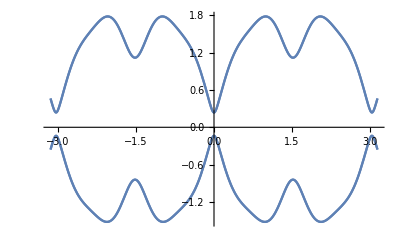

```mathematica
Plot[Eigenvalues[H12[{k,0,0}]],{k,-Pi,Pi}]
```

```mathematica
H32[kbar_]:=KroneckerProduct[PauliTop,PauliMatrix[0]*(e5+aii[kbar,t55a,t55b])]+KroneckerProduct[PauliBottom,PauliMatrix[0]*(e7+aii[kbar,t77a,t77b])]+KroneckerProduct[PauliPlus,I*b57[kbar]*PauliTop+I*Conjugate[b57[kbar]]*PauliBottom+I*b58[kbar]*PauliPlus-I*Conjugate[b58[kbar]]*PauliMinus]+Transpose[Conjugate[KroneckerProduct[PauliPlus,I*b57[kbar]*PauliTop+I*Conjugate[b57[kbar]]*PauliBottom+I*b58[kbar]*PauliPlus-I*Conjugate[b58[kbar]]*PauliMinus]]];
```

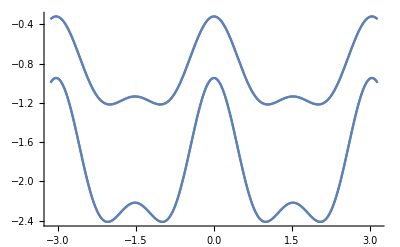

```mathematica
Plot[Eigenvalues[H32[{k,0,0}]],{k,-Pi,Pi}]
```

```mathematica
Hint[kbar_]:=KroneckerProduct[PauliTop,g15[kbar]]+KroneckerProduct[PauliBottom,g37[kbar]]+KroneckerProduct[PauliPlus,g17[kbar]]+KroneckerProduct[PauliMinus,g35[kbar]];
```

```mathematica
Hfull[kbar_]:=KroneckerProduct[PauliTop,H12[kbar]]+KroneckerProduct[PauliBottom,H32[kbar]]+KroneckerProduct[PauliPlus,Hint[kbar]]+KroneckerProduct[PauliMinus,ConjugateTranspose[Hint[kbar]]];
```

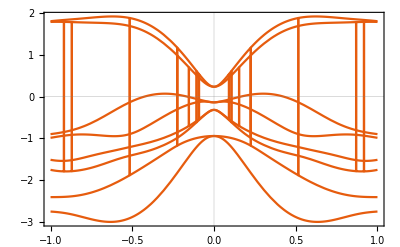

```mathematica
Plot[Eigenvalues[Hfull[{k,0,0}]],{k,-1,1},PlotTheme->"Scientific"]
```

Expand the full hamiltonian to second order in kx

```mathematica
Hfullreal=Simplify[Hfull[{kx,0,0}],Assumptions->Element[kx,Reals]];
Hfullorder2=Normal[Series[Hfullreal,{kx,0,2}]];
```

Check to see if the features remain

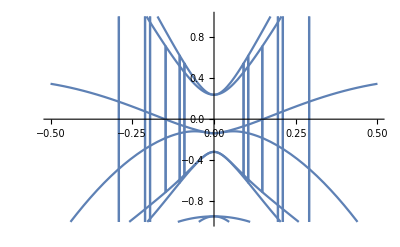

```mathematica
Plot[Eigenvalues[Hfullorder2],{kx,-0.5,0.5},PlotRange->{{-1,1}}]
```

This is what the Hamiltonian looks like

```mathematica
Normal[Series[Simplify[Hfull[{kx,0.,0}],Assumptions->Element[kx,Reals]],{kx,0,2}]]//MatrixForm
```

(-0.137+(3.57361+0. ⅈ) kx^2 | 0 | (4.44089×10^-16-2.8727×10^-17 ⅈ) kx | (-1.50584-3.3534 ⅈ) kx | (0.0860483+2.12382 ⅈ) kx | (0.0860483+2.12382 ⅈ) kx | (-3.46945×10^-17+1.9082×10^-17 ⅈ)+(1.74824-0.102838 ⅈ) kx^2 | (-2.08167×10^-17+3.90313×10^-18 ⅈ)-(1.74824+0.102838 ⅈ) kx^2
0 | -0.137+(3.57361+0. ⅈ) kx^2 | (-1.50584+3.3534 ⅈ) kx | 0 | (0.0860483-2.12382 ⅈ) kx | (-0.0860483+2.12382 ⅈ) kx | (-3.46945×10^-17+1.9082×10^-17 ⅈ)+(1.74824-0.102838 ⅈ) kx^2 | (2.08167×10^-17-3.90313×10^-18 ⅈ)+(1.74824+0.102838 ⅈ) kx^2
0 | (-1.50584-3.3534 ⅈ) kx | 0.238-(3.21367+0. ⅈ) kx^2 | 0 | (0.+2.77556×10^-17 ⅈ)-(1.58113-4.16255×10^-16 ⅈ) kx^2 | 1.58113 kx^2 | (-0.788776+2.3598 ⅈ) kx | (-0.788776+2.3598 ⅈ) kx
(-1.50584+3.3534 ⅈ) kx | (-4.44089×10^-16+2.8727×10^-17 ⅈ) kx | 0 | 0.238-(3.21367+0. ⅈ) kx^2 | (0.+2.77556×10^-17 ⅈ)-(1.58113-4.16255×10^-16 ⅈ) kx^2 | -1.58113 kx^2 | (0.788776+2.3598 ⅈ) kx | (0.788776+2.3598 ⅈ) kx
(0.0860483-2.12382 ⅈ) kx | (0.0860483+2.12382 ⅈ) kx | (0.-2.77556×10^-17 ⅈ)-(1.58113+4.16255×10^-16 ⅈ) kx^2 | (0.-2.77556×10^-17 ⅈ)-(1.58113+4.16255×10^-16 ⅈ) kx^2 | -0.3184-(2.50238+0. ⅈ) kx^2 | 0 | 0.+0. ⅈ | 0
(0.0860483-2.12382 ⅈ) kx | (-0.0860483-2.12382 ⅈ) kx | (0.-2.77556×10^-17 ⅈ)+(1.58113-4.16255×10^-16 ⅈ) kx^2 | (0.+2.77556×10^-17 ⅈ)-(1.58113-4.16255×10^-16 ⅈ) kx^2 | 0 | -0.3184-(2.50238+0. ⅈ) kx^2 | 0 | 0.+0. ⅈ
(-3.46945×10^-17-1.9082×10^-17 ⅈ)+(1.74824+0.102838 ⅈ) kx^2 | (-3.46945×10^-17-1.9082×10^-17 ⅈ)+(1.74824+0.102838 ⅈ) kx^2 | (-0.788776-2.3598 ⅈ) kx | (0.788776-2.3598 ⅈ) kx | 0.+0. ⅈ | 0 | -0.946-(4.29347+0. ⅈ) kx^2 | 0
(3.46945×10^-17-1.9082×10^-17 ⅈ)-(1.74824-0.102838 ⅈ) kx^2 | (-3.46945×10^-17+1.9082×10^-17 ⅈ)+(1.74824-0.102838 ⅈ) kx^2 | (-0.788776-2.3598 ⅈ) kx | (0.788776-2.3598 ⅈ) kx | 0 | 0.+0. ⅈ | 0 | -0.946-(4.29347+0. ⅈ) kx^2)

Define the blocks to construct an effective 4x4 model

```mathematica
Hint2=({{(0.08604828412002194-2.1238200000000003 ⅈ) kx, (0.08604828412002176+2.1238200000000003 ⅈ) kx, (0.-2.7755575615628914*^-17 ⅈ)-(1.5811281+4.162545308439291*^-16 ⅈ) kx^2, (0.-2.7755575615628914*^-17 ⅈ)-(1.5811281+4.162545308439291*^-16 ⅈ) kx^2}, {(0.08604828412002176-2.1238200000000003 ⅈ) kx, (-0.08604828412002194-2.1238200000000003 ⅈ) kx, (0.-2.7755575615628914*^-17 ⅈ)+(1.5811281-4.162545308439291*^-16 ⅈ) kx^2, (0.+2.7755575615628914*^-17 ⅈ)-(1.5811281-4.162545308439291*^-16 ⅈ) kx^2}, {(1.7482392000000002+0.10283760000000072 ⅈ) kx^2, (-3.469446951953614*^-17-1.9081958235744878*^-17 ⅈ)+(1.7482392000000002+0.10283760000000072 ⅈ) kx^2, (-0.7887759377668665-2.3598 ⅈ) kx, (0.7887759377668668-2.3598 ⅈ) kx}, {-(1.7482392000000002-0.10283760000000072 ⅈ) kx^2, (-3.469446951953614*^-17+1.9081958235744878*^-17 ⅈ)+(1.7482392000000002-0.10283760000000072 ⅈ) kx^2, (-0.7887759377668668-2.3598 ⅈ) kx, (0.7887759377668665-2.3598 ⅈ) kx}});
H122=({{-0.13700000000000012+(3.5736066+0. ⅈ) kx^2, 0, (4.440892098500626*^-16-2.8727020762175923*^-17 ⅈ) kx, (-1.5058449721003822-3.3533999999999997 ⅈ) kx}, {0, -0.13700000000000012+(3.5736066+0. ⅈ) kx^2, (-1.5058449721003822+3.3533999999999997 ⅈ) kx, 0}, {0, (-1.5058449721003822-3.3533999999999997 ⅈ) kx, 0.2380000000000001-(3.2136749999999994+0. ⅈ) kx^2, 0}, {(-1.5058449721003822+3.3533999999999997 ⅈ) kx, (-4.440892098500626*^-16+2.8727020762175923*^-17 ⅈ) kx, 0, 0.2380000000000001-(3.2136749999999994+0. ⅈ) kx^2}});
H322=({{-0.3183999999999999-(2.5023815999999997+0. ⅈ) kx^2, 0, 0.+0. ⅈ, 0}, {0, -0.3183999999999999-(2.5023815999999997+0. ⅈ) kx^2, 0, 0.+0. ⅈ}, {0.+0. ⅈ, 0, -0.946-(4.2934698+0. ⅈ) kx^2, 0}, {0, 0.+0. ⅈ, 0, -0.946-(4.2934698+0. ⅈ) kx^2}});
Heff2=H122-Hint2.Inverse[H322].ConjugateTranspose[Hint2];
```

Expand this model to 4th order (2nd order does not yield the same features here)

```mathematica
Heff22=Normal[Series[Simplify[Heff2,Assumptions->Element[kx,Reals]],{kx,0,4}]];
```

```mathematica
Heff22//MatrixForm
```

(-0.137+(31.9531+0. ⅈ) kx^2-(217.756+0. ⅈ) kx^4 | 0. | (4.45904×10^-16-2.54992×10^-16 ⅈ) kx+(0.944931-7.94384 ⅈ) kx^3 | (-1.50584-3.3534 ⅈ) kx-(1.37191-15.4343 ⅈ) kx^3
0. | -0.137+(31.9531+0. ⅈ) kx^2-(217.756+0. ⅈ) kx^4 | (-1.50584+3.3534 ⅈ) kx-(4.00861+23.3225 ⅈ) kx^3 | (-1.17906×10^-16+2.82864×10^-16 ⅈ) kx-(3.58162+0.0555842 ⅈ) kx^3
(1.81431×10^-18+2.26265×10^-16 ⅈ) kx+(0.944931+7.94384 ⅈ) kx^3 | (-1.50584-3.3534 ⅈ) kx-(4.00861-23.3225 ⅈ) kx^3 | (0.238+2.3568×10^-49 ⅈ)+(9.87475-3.06299×10^-32 ⅈ) kx^2-(40.1379-5.5044×10^-17 ⅈ) kx^4 | (2.63689×10^-33+4.15853×10^-33 ⅈ)+(13.0884+1.6458×10^-15 ⅈ) kx^2-(59.4025+6.72356×10^-15 ⅈ) kx^4
(-1.50584+3.3534 ⅈ) kx-(1.37191+15.4343 ⅈ) kx^3 | (-5.61995×10^-16-2.54137×10^-16 ⅈ) kx-(3.58162-0.0555842 ⅈ) kx^3 | (2.63689×10^-33-4.15853×10^-33 ⅈ)+(13.0884-1.6458×10^-15 ⅈ) kx^2-(59.4025-6.72356×10^-15 ⅈ) kx^4 | (0.238-2.3568×10^-49 ⅈ)+(9.87475+3.06299×10^-32 ⅈ) kx^2-(40.1379+5.5044×10^-17 ⅈ) kx^4)

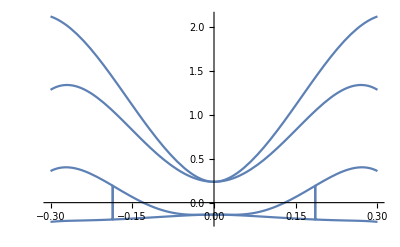

```mathematica
Plot[Eigenvalues[Heff22],{kx,-0.3,0.3}]
```

Tune these parameters to arrive at a concise model.

Schrieffer-wolf effective Hamiltonian

```mathematica
H1=ConjugateTranspose[Hint[{kx,0,0}]].Inverse[H32[{kx,0,0}]].Hint[{kx,0,0}];
Normal[Series[Simplify[H1],Assumptions->Element[kx,Reals]],{kx,0,2}]
```

```mathematica
H1simp=Simplify[H1,Assumptions->Element[kx,Reals]]
```

```mathematica
H1simp2=Normal[Series[H1simp,{kx,0,4}]];
H0simp2=Normal[Series[Simplify[H12[{kx,0,0}],Assumptions->Element[kx,Reals]],{kx,0,4}]];
Hsimp2=H0simp2-H1simp2;
```

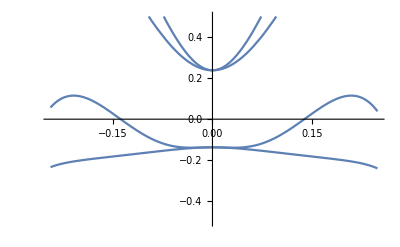

```mathematica
Plot[Eigenvalues[Hsimp2],{kx,-0.5,0.5},PlotRange->{-0.5,0.5}]
```

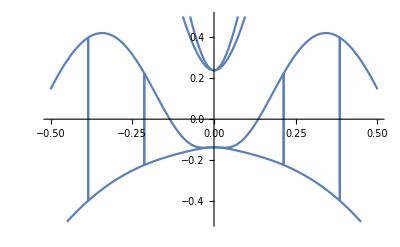

```mathematica
Plot[Eigenvalues[H12[{kx,0,0}]-H1],{kx,-0.5,0.5},PlotRange->{-0.5,0.5}]
```

```mathematica
Chop[FullSimplify[Hsimp2]]//MatrixForm
```

```mathematica
({{-0.13700000000000012+31.95310220050253 kx^2-342.889224571148 kx^4, 0, (-2.780361259803016-7.943842283914085 ⅈ) kx^3, (-1.505844972100382-3.3533999999999993 ⅈ) kx-(0.29651382593833264-22.618754927788316 ⅈ) kx^3}, {0, -0.13700000000000012+31.95310220050253 kx^2-342.88922457114813 kx^4, kx ((-1.5058449721004852+3.3534000000000836 ⅈ)-(2.933206848782281+30.507013046988373 ⅈ) kx^2), (0.14366823695514253-0.05558416471747049 ⅈ) kx^3}, {(-2.7803612598030156+7.943842283914088 ⅈ) kx^3, (-1.505844972100382-3.3534 ⅈ) kx-(2.9332068487862157-30.507013046984937 ⅈ) kx^3, 0.2380000000000001+9.874746818181821 kx^2-89.11227148348571 kx^4, 13.08842181818182 kx^2-111.72758558243632 kx^4}, {kx ((-21.50584+3.3533999999999997 ⅈ)-(0.29651382593912934+22.618754927788075 ⅈ) kx^2), (0.1436682369551443+0.05558416471746558 ⅈ) kx^3, kx^2 (13.088421818182027-111.72758558244048 kx^2), 0.2380000000000001+9.874746818181821 kx^2-89.11227148348557 kx^4}})
```

```mathematica
Hsimp2mod[kx_,m_,aa_,bb_,cc_,dd_,ff_,gg_,α1_,α2_,α3_,α4_,α5_]:={{-m+aa*kx^2-bb*kx^4,0,Conjugate[α1]*kx^3,Conjugate[α2]*kx-Conjugate[α3]*kx^3},{0,-m+aa*kx^2-bb*kx^4,α2*kx-Conjugate[α4]*kx^3,Conjugate[α5]*kx^3},{α1*kx^3,Conjugate[α2]*kx-α4*kx^3,m+cc*kx^2-dd*kx^4,ff*kx^2-gg*kx^4},{α2*kx-α3*kx^3,α5*kx^3,ff*kx^2-gg*kx^4,m+cc*kx^2-dd*kx^4}};
Manipulate[Plot[Eigenvalues[Hsimp2mod[kx,m,aa,bb,cc,dd,ff,gg,0,(-1.5058449721003557*0-I*α1 ),(0.29651382593912934*0-I*α3 ),(2.9332068487862157*0-I*α3),0]],{kx,-0.5,0.5},PlotRange->{-1,1},PlotTheme->"Scientific"],{{m,0.2},-1,1},{{aa,10},-50,50},{{bb,0},-400,400},{{cc,0},-20,20},{{dd,0},-200,200},{{ff,0},-20,20},{{gg,0},-200,200},{{α1,3},-5,5},{{α3,30},-50,50}]
```

```mathematica
Hsimp2mod[kx,m,aa,bb,cc,dd,ff,gg,α1,α2,α3,α4,α5]//MatrixForm
```

(aa kx^2-bb kx^4-m | 0 | kx^3 Conjugate[α1] | kx α2-kx^3 Conjugate[α3]
0 | aa kx^2-bb kx^4-m | kx Conjugate[α2]-kx^3 Conjugate[α4] | kx^3 Conjugate[α5]
kx^3 α1 | -kx^3 α4+kx Conjugate[α2] | cc kx^2-dd kx^4+m | ff kx^2-gg kx^4
kx α2-kx^3 α3 | kx^3 α5 | ff kx^2-gg kx^4 | cc kx^2-dd kx^4+m)

```mathematica
Manipulate[Plot[{aa*kx^2+Sqrt[(m)^2+kx^2*(aa1-aa3*kx^2)^2],aa*kx^2-Sqrt[m^2+kx^2*(aa1-aa3*kx^2)^2]},{kx,-1,1},PlotRange->{-1,1}],{aa,-10,10},{m,-1,1},{aa1,-5,5},{aa3,-20,20}]
```

Effective  Hamiltonian

```mathematica
Heff[kbar_]:=H12[kbar]-Transpose[Conjugate[Hint[kbar]]].Inverse[H32[kbar]].Hint[kbar];
```

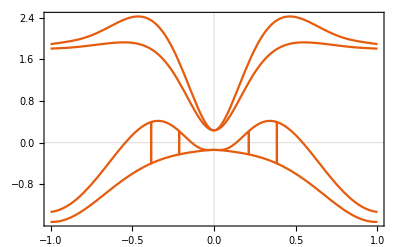

```mathematica
Plot[Eigenvalues[Heff[{k,0,0}]],{k,-1,1},PlotTheme->"Scientific"]
```

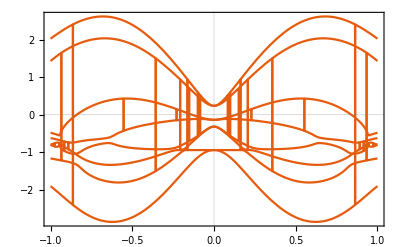

```mathematica
HfullOrder2[kx_]:=Normal[Series[Hfull[{k,0,0}],{k,0,1}]]/.k->kx;
Plot[Re[Eigenvalues[HfullOrder2[kx]]],{kx,-1,1},PlotTheme->"Scientific"]
```

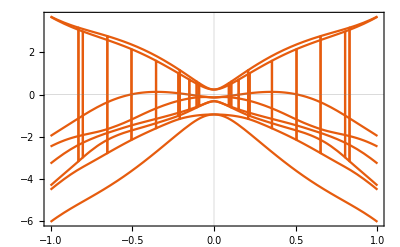

```mathematica
HfullOrder2[kx_]:=Normal[Series[Hfull[{k,0,0}],{k,0,2}]]/.k->kx;
Plot[Re[Eigenvalues[HfullOrder2[kx]]],{kx,-1,1},PlotTheme->"Scientific"]
```

1st order SW Hamiltonian (analytic)
Find the wavefunctions and energies

```mathematica
TR=KroneckerProduct[PauliMatrix[0],I*PauliMatrix[2]];
Htr={{m11,m12,m13,m14},{m21,m22,m23,m24},{m31,m32,m33,m34},{m41,m42,m43,m44}};
```

```mathematica
TR.Htr.Inverse[TR]//MatrixForm
```

(m22 | -m21 | m24 | -m23
-m12 | m11 | -m14 | m13
m42 | -m41 | m44 | -m43
-m32 | m31 | -m34 | m33)

They are also conjugated and k -> -k.